```mathematica
ClearAll[Data,UpData]
```

```mathematica
UpData=Import["C:\\Users\\Gentlen\\Dysk Google\\Fizyka\\Term 6th\\Pracownia II\\PR\\spd.txt","Table",NumberPoint->","];
Data=Transpose[UpData];
```

```mathematica
Length[Data]
```

12

```mathematica
PlotData=Table[Transpose[{Data[[1]],Data[[i]]}],{i,2,Length[Data]}];
```

```mathematica
Plots=ListLinePlot[#,AxesLabel->{"θ","I [imp/s]"}]&/@PlotData;
```

```mathematica
FitRanges={{12,14},{11,13.5},{9.8,11},{8.5,10.5},{8,10},{7.2,9},{6.5,8},{6.4,7.4},{6.2,7},{6,7.5},{5.5,7.2}}
Fits=Table[Fit[Select[PlotData[[i]],#[[1]]≥FitRanges[[i]][[1]]&&#[[1]]<=FitRanges[[i]][[2]]&],{1,x},x],{i,1,11}];
Comparison=Transpose[{FitRanges,Fits,Plots,Zeroλ}];
```

{{12,14},{11,13.5},{9.8,11},{8.5,10.5},{8,10},{7.2,9},{6.5,8},{6.4,7.4},{6.2,7},{6,7.5},{5.5,7.2}}

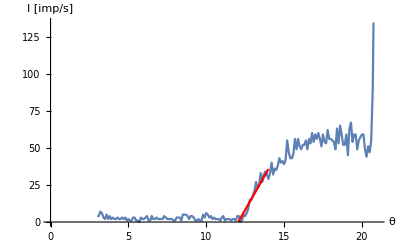
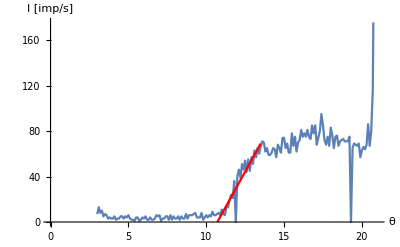
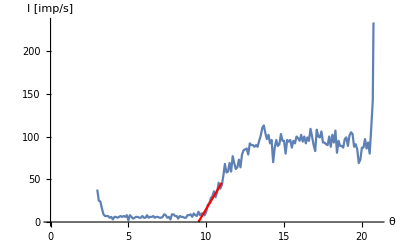
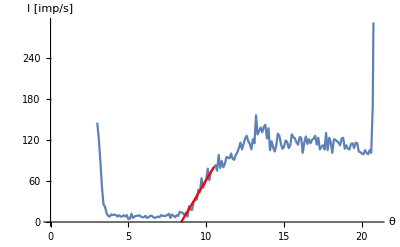
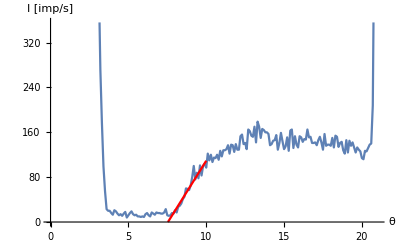
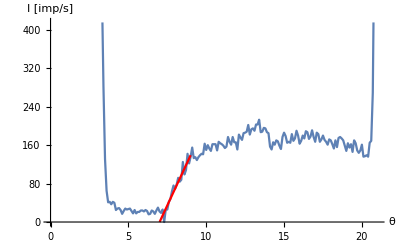
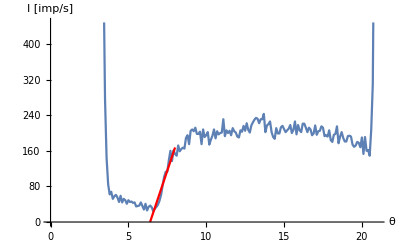
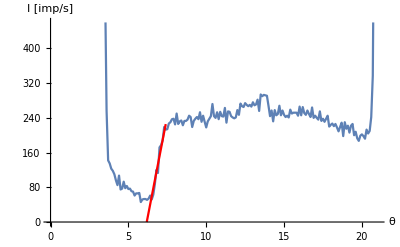

```mathematica
FitPlot=Show[#[[3]],Plot[#[[2]],{x,#[[4]][[1]][[1]][[2]],#[[1]][[2]]},PlotStyle->Red]]&/@Comparison
```

```mathematica
Export["C:\\Users\\Gentlen\\Dysk Google\\Fizyka\\Term 6th\\Pracownia II\\PR\\allfits.pdf",Show[FitPlot,PlotRange->{0,700}]]
```

C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\PR\allfits.pdf

```mathematica
Fits
```

{-221.732+18.3896 x,-265.72+24.7966 x,-290.176+30.5495 x,-321.874+38.3377 x,-335.281+44.4545 x,-488.358+69.7193 x,-666.926+104.309 x,-1143.32+185. x,-1344.62+230.667 x,-1032.04+200.015 x,-1000.63+214.334 x}

FittedModel[3.08933 x]

3.08933 x

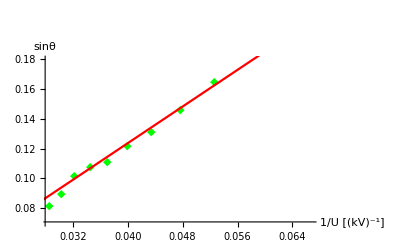

C:\Users\Gentlen\Dysk Google\Fizyka\Term 6th\Pracownia II\PR\fitsin.pdf

```mathematica
PlanckData=Table[{1/(15+2(i-1)),Sins[[i]][[1]]},{i,1,11}];
linmod=LinearModelFit[PlanckData,x,x,IncludeConstantBasis->False]
ehc=Normal[linmod]
fitsin=Show[ListPlot[PlanckData,AxesLabel->{"1/U [(kV)^-1]","sinθ"},PlotRange->{0.07,0.18},PlotMarkers->{"◆"},PlotStyle->Green],Plot[ehc,{x,0,0.065},PlotStyle->Red]]
Export["C:\\Users\\Gentlen\\Dysk Google\\Fizyka\\Term 6th\\Pracownia II\\PR\\fitsin.pdf",fitsin]
```

```mathematica
h=6.62607004 10^-34
e=1.60217662 10^-19
c=299792458
d=402.8/2 10^-12
ehc[[1]]*(2 e d)/c*10^3
%/h-1
```

6.62607×10^-34

1.60218×10^-19

299792458

2.014×10^-10

6.65033×10^-34

0.00366167

```mathematica
linmod["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 0.207759 | 0.207759 | 17226.3 | 1.61802×10^-17
Error | 10 | 0.000120606 | 0.0000120606 |  | 
Total | 11 | 0.20788 |  |  |

```mathematica
linmod["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
x | 3.08933 | 0.0235379 | 131.249 | 1.61802×10^-17

```mathematica
ehc[[1]]-Mod[ehc[[1]],0.01]+0.01
```

3.08

```mathematica
(2 d e)/c 0.023 10^3
```

4.95116×10^-36

```mathematica
Zeroλ=NSolve[#==0,x]&/@Fits
```

{{{x→12.0574}},{{x→10.716}},{{x→9.49856}},{{x→8.39578}},{{x→7.54212}},{{x→7.00463}},{{x→6.39377}},{{x→6.1801}},{{x→5.82929}},{{x→5.1598}},{{x→4.66857}}}

```mathematica
Sins=Sin[(x π)/180/.#]&/@Zeroλ
```

{{0.208892},{0.185941},{0.165023},{0.14601},{0.131255},{0.12195},{0.111361},{0.107654},{0.101565},{0.0899339},{0.0813917}}

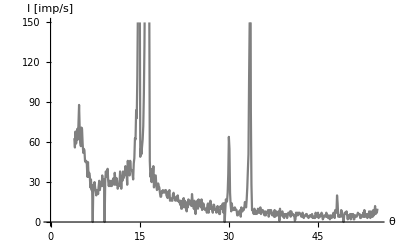

-Graphics-

```mathematica
NaClDataRaw=Import["C:\\Users\\Gentlen\\Dysk Google\\Fizyka\\Term 6th\\Pracownia II\\PR\\nacl.dat","Table",NumberPoint->","];
NaClData=NaClDataRaw[[4;;Length[NaClDataRaw]]];
ListLinePlot[NaClData,PlotRange->{0,150},AxesLabel->{"θ","I [imp/s]"},PlotStyle->Gray]
```

```mathematica
FindMaxIinInterval[Dane_,Int0_,IntF_]:=MaximalBy[Select[Dane,#[[1]]≥Int0&&#[[1]]<=IntF&],Last]
```

Alfa

```mathematica
FindMaxIinInterval[NaClData,16,17.2]
FindMaxIinInterval[NaClData,32,34]
```

{{16.5,1199.}}

{{33.6,272.}}

Beta

```mathematica
FindMaxIinInterval[NaClData,13,15.5]
FindMaxIinInterval[NaClData,29,31]
FindMaxIinInterval[NaClData,47,49]
```

{{14.9,325.}}

{{30.,64.}}

{{48.2,20.}}

```mathematica
la=154.05 10^-12
lb=139.23 10^-12
katy=Sin[#*π/180]&/@{16.5,33.6,14.9,30,48.2}
rzedy={1,2,1,2,3}
df={la,la,lb,lb,lb}
dm=Transpose[{katy,rzedy,df}]
```

1.5405×10^-10

1.3923×10^-10

{0.284015,0.553392,0.257133,1/2,0.745476}

{1,2,1,2,3}

{1.5405×10^-10,1.5405×10^-10,1.3923×10^-10,1.3923×10^-10,1.3923×10^-10}

{{0.284015,1,1.5405×10^-10},{0.553392,2,1.5405×10^-10},{0.257133,1,1.3923×10^-10},{1/2,2,1.3923×10^-10},{0.745476,3,1.3923×10^-10}}

```mathematica
dm//TableForm
```

0.284015 | 1 | 1.5405×10^-10
0.553392 | 2 | 1.5405×10^-10
0.257133 | 1 | 1.3923×10^-10
1/2 | 2 | 1.3923×10^-10
0.745476 | 3 | 1.3923×10^-10

```mathematica
dm[[1]]
```

{0.284015,1,1.5405×10^-10}

```mathematica
Wyniki=Table[(dm[[i]][[2]]dm[[i]][[3]])/(dm[[i]][[1]]),{i,1,Length[dm]}]
```

{5.424×10^-10,5.56749×10^-10,5.41471×10^-10,5.5692×10^-10,5.603×10^-10}

```mathematica
Srednia=Sum[Wyniki[[i]],{i,1,Length[Wyniki]}]/Length[Wyniki]
```

5.51568×10^-10

```mathematica
√(Sum[(Wyniki[[i]]-Srednia)^2,{i,1,Length[Wyniki]}]/(Length[Wyniki](Length[Wyniki]-1)))
```

3.98572×10^-12

```mathematica
2 Srednia
```

5.51568×10^-10

```mathematica
5.641/5.52
```

1.02192